LogSeriesDistribution[1.57974×10^-11]

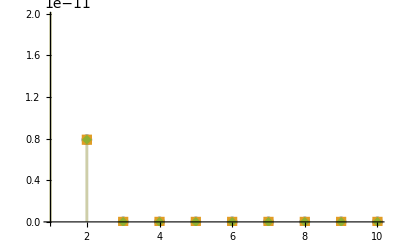

```mathematica
ClearAll["Global`*"]
ClearSystemCache[];
$HistoryLength = 0;
PATHPREFIX="/home/david/Documents/digital-twins/ton.iot/processed/";
IMAGEPREFIX="images/root_toniot_synthetic_";
(* Read individual files of 2 data columns each. *)
fitTimeseriesModel[f_,d_,y_,z_]:=Module[{fname=f,data=d,yaxis=y,colnum=z},
dataset=Select[data[[All,{1,z}]],#[[2]]>0 &];
xtime=dataset[[All,2]]; (* Utc_timestamp *)
xtime=Subtract[xtime,xtime[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{xtime}]; (* is 2 because only 2 columns read *)
plotFile=StringJoin[PATHPREFIX,IMAGEPREFIX,StringDrop[fname,-4],"-",yaxis,".png"];
(*Print[plotFile];*)
Export[plotFile,ListPlot[dataset[[All,2]],PlotLabel->yaxis,AxesLabel->{"Time.offset",yaxis},ImageSize->700]];
dataR=TimeSeries[timeseries,TemporalRegularity->True];
atsm=TimeSeriesModelFit[dataR];
process=Normal[atsm];
Print[process];
(*Print[CovarianceFunction[process,s,t]];
Print[TimeSeriesForecast[process,dataset[[All,2]], 2]];*)
];
(***********************************************)
(* In general whether or not you have causal series, the only time you would be justified or correct in taking the Log of Y is when it can be proven that the Variance of Y is proportional to the Expected Value of Y^2 . What is important is the relationship between the inputs and outputs,not the distribution of the inputs themselves. *)
fitBinaryTimeseriesModel[f_,d_,y_,z_]:=Module[{fname=f,data=d,yaxis=y,colnum=z},
dataset=Select[data[[All,{1,z}]],#[[2]]>0 &];
xtime=dataset[[All,1]];
xtime=Subtract[xtime,xtime[[1]]];
timeseries=TimeSeries[dataset[[All,2]],{xtime}];
lsd=FindDistribution[dataset[[All,2]]];
Print[lsd];
(*Print[PDF[lsd,k]];*)
(* y_{dt}=Bernoulli(logit(x_t)); x_t=ARIMA(p,d,q) *)
(*Print[DiscretePlot[Table[PDF[dataset[[All,2]],k],PlotLabel->fname,AxesLabel->{"Time.offset",yaxis}]]];*)
Print[DiscretePlot[Table[PDF[lsd,k],{θ,{0.5,0.8,0.99}}]//Evaluate,{k,10},PlotMarkers->Automatic]];
(*atsm=TimeSeriesModelFit[timeseries];
process=Normal[atsm];
Print[process];
model=LinearModelFit[timeseries,x,x];
Print[model["BestFit"]];
Show[ListPlot[timeseries],Plot[model["BestFit"],{x,0,300000}],Frame->True]
*)
];
(***********************************************)
headerList={"Datetime", "Utc_timestamp", "Current_temperature","Thermostat_status"};
theFile="IoT_Thermostat.csv" ;
xdataset=Import[StringJoin[PATHPREFIX,theFile],{"CSV","Data",All},"HeaderLines"->1,"FieldSeparators"->",",MissingDataRules->{"."->Missing[],""->Missing[]}];
(*fitTimeseriesModel[theFile, xdataset, headerList[[3]],3]; *)
fitBinaryTimeseriesModel[theFile, xdataset, headerList[[4]],4]; 
(***********************************************)
```